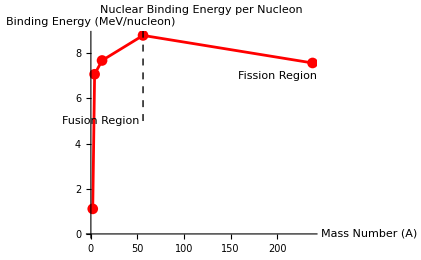

```mathematica
ListLinePlot[bindingData,PlotStyle->Red,PlotMarkers->Automatic,PlotLabel->"Nuclear Binding Energy per Nucleon",AxesLabel->{"Mass Number (A)","Binding Energy (MeV/nucleon)"},Epilog->{Text["Fusion Region",{10,5},{-1,0}],Text["Fission Region",{200,7},{1,0}],Dashed,Line[{{56,5},{56,9}}]}]
```

# La Fission Nucléaire : Réacteurs Actuels, Générations Futures et Réacteurs au Thorium

Sommaire

1. Introduction à la fission nucléaire
2. Les réacteurs nucléaires actuels
3. Les réacteurs de nouvelle génération
4. Les réacteurs au Thorium

## Introduction à la fission nucléaire

La fission nucléaire est un phénomène physique au cœur de la production d'énergie nucléaire. Découverte en 1938 par Otto Hahn et Fritz Strassmann, et théorisée par Lise Meitner et Otto Frisch, la fission est le processus par lequel un noyau atomique lourd, comme celui de l'uranium-235 ou du plutonium-239, se divise en deux noyaux plus légers, libérant ainsi une quantité considérable d'énergie sous forme de chaleur et de rayonnement. 

Ce processus est accompagné de l'émission de plusieurs neutrons libres. Ces neutrons, à leur tour, peuvent provoquer la fission d'autres noyaux voisins, déclenchant une réaction en chaîne contrôlée dans les réacteurs nucléaires civils. Cette réaction permet de maintenir une production stable d'énergie thermique, transformée ensuite en énergie électrique via un circuit de conversion.

Figure 1 : Schéma illustrant la fission d'un noyau d'uranium-235 après absorption d'un neutron, avec émission de neutrons secondaires et libération d'énergie.

```mathematica
Graphics3D[{Sphere[{0,0,0},1],Arrow[{{0,0,0},{2,0,0}}],Sphere[{3,0,0},0.5],Sphere[{-3,0,0},0.5],Text["Noyau initial",{0,0,1.2}],Text["Neutron incident",{1,0.2,0}],Text["Fragments de fission",{3.5,0,0}]},Boxed->False,Axes->False]
```

-Graphics3D-

Figure 2 : Représentation 3D simplifiée de la fission nucléaire, illustrant le noyau initial, le neutron incident, et les fragments de fission résultants.

## Les réacteurs nucléaires actuels

Les réacteurs nucléaires actuels, principalement de générations II et III, sont le pilier de la production d'électricité nucléaire dans le monde. La majorité d'entre eux utilisent de l'uranium enrichi comme combustible et emploient l'eau comme modérateur et fluide caloporteur.

Parmi ces technologies, les réacteurs à eau pressurisée (REP) dominent. Dans un REP, l'eau sous haute pression empêche l'ébullition du liquide malgré des températures supérieures à 300°C. La chaleur générée dans le cœur du réacteur est transférée à un circuit secondaire où elle transforme de l'eau en vapeur pour entraîner des turbines électriques.

Figure 3 : Schéma d'un réacteur à eau pressurisée (REP). La chaleur est transférée du réacteur vers un générateur de vapeur qui alimente la turbine électrique.

```mathematica
Graphics3D[{Cylinder[{{0,0,0},{0,0,4}},1],Style[Text["Cœur du réacteur",{0,0,4.5}],Bold],Cylinder[{{3,0,0},{3,0,4}},0.5],Style[Text["Générateur de vapeur",{3,0,4.5}],Bold],Arrow[{{1,0,2},{2.5,0,2}}],Text["Circuit primaire",{1.8,0.2,2.2}]},Boxed->False]
```

-Graphics3D-

Figure 4 : Modélisation 3D simplifiée du circuit primaire d'un REP, illustrant le transfert de chaleur du cœur du réacteur vers le générateur de vapeur.

La sûreté nucléaire repose sur plusieurs systèmes de défense en profondeur : barres de contrôle pour arrêter la réaction en chaîne, enceinte de confinement pour limiter les fuites radioactives, et multiples circuits de refroidissement redondants. Ces dispositifs permettent de minimiser les risques d'accident majeur.

## Les réacteurs de nouvelle génération

La quatrième génération de réacteurs nucléaires vise à répondre aux défis de durabilité, de sûreté et de gestion des ressources. Ces réacteurs sont conçus pour exploiter plus efficacement le combustible nucléaire et réduire la quantité de déchets radioactifs produits.

Les réacteurs à neutrons rapides refroidis au sodium, par exemple, permettent de recycler le combustible nucléaire en utilisant le plutonium et les actinides mineurs, réduisant ainsi la charge des déchets à long terme. Les réacteurs à sels fondus, eux, fonctionnent avec un combustible liquide, ce qui permet une meilleure gestion des réactions et une sûreté passive accrue grâce à des mécanismes de drainage du combustible en cas de surchauffe.

Figure 5 : Schéma d'un réacteur à sels fondus, montrant le circuit du combustible liquide et les systèmes de sécurité passifs.

```mathematica
GraphicsGrid[{{BarChart[{50,70,85},ChartLabels->{"Gén. II","Gén. III","Gén. IV"},PlotLabel->"Comparaison du rendement (%) des générations de réacteurs",ChartStyle->"Pastel"],PieChart[{30,40,30},ChartLabels->{"Actinides","Produits de fission","Déchets courts"},PlotLabel->"Répartition des déchets générés",ChartStyle->"Pastel"]}}]
```

-Graphics-

Figure 6 : Graphiques comparatifs illustrant les améliorations de rendement et la gestion des déchets dans les réacteurs de génération IV.

Outre les gains de rendement et la réduction des déchets, la génération IV explore également des cycles du combustible innovants et des systèmes de production de chaleur à très haute température pour des applications industrielles telles que la production d'hydrogène ou la désalinisation de l'eau de mer.

## Les réacteurs au Thorium

Le thorium, bien que peu utilisé aujourd'hui, représente une alternative prometteuse à l'uranium. Abondant dans la croûte terrestre, il ne nécessite pas d'enrichissement et peut produire de l'énergie nucléaire après conversion en uranium-233 fissile.

Dans les réacteurs à sels fondus au thorium, le combustible liquide permet d'intégrer la sûreté passive et la flexibilité opérationnelle. Le cycle thorium-uranium génère moins d'actinides mineurs, contribuant ainsi à la réduction de la durée de vie des déchets nucléaires.

Figure 7 : Cycle du combustible au thorium, montrant la conversion du thorium-232 en uranium-233 fissile par capture neutronique.

```mathematica
Graphics3D[{Sphere[{0,0,0},1],Style[Text["Cœur de sel fondu",{0,0,1.5}],Bold],Tube[{{1,0,0},{3,0,0}},0.1],Sphere[{3,0,0},0.5],Text["Échangeur de chaleur",{3,0,0.8}],Arrow[{{3,0,0.5},{4,0,0.5}}],Text["Production de vapeur",{4.2,0,0.5}]},Boxed->False,Lighting->"Neutral"]
```

-Graphics3D-

Figure 8 : Modélisation 3D d'un réacteur à sels fondus utilisant le thorium, avec le circuit de transfert de chaleur vers la production de vapeur.

L'avenir du thorium dépendra de la résolution des défis technologiques actuels, notamment la résistance des matériaux face aux sels fondus corrosifs et le développement d'une chaîne d'approvisionnement dédiée. Néanmoins, ses avantages environnementaux et ses perspectives de sûreté en font une option sérieusement envisagée pour un nucléaire durable.

```mathematica
ARE : Fusion et Armes
Partie 1 : La Fusion Nucléaire - État de l’Art et Défis Technologiques
Introduction à la Fusion Nucléaire
La fusion nucléaire est la réaction qui alimente les étoiles, où des noyaux légers s’unissent pour former des noyaux plus lourds, libérant une énergie considérable. Contrairement à la fission, la fusion offre:

Des combustibles quasi-illimités (deutérium dans l’eau de mer, lithium pour le tritium)

Pas de déchets hautement radioactifs à vie longue

Sécurité intrinsèque (pas de réaction en chaîne incontrôlable)
```

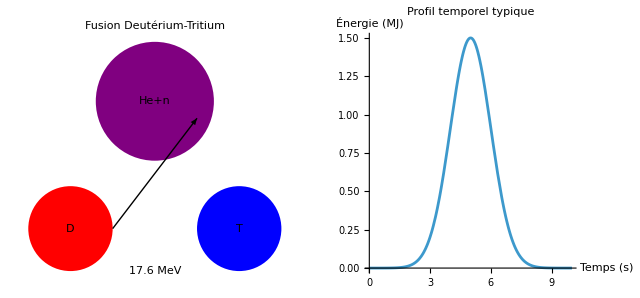

```mathematica
(*Visualisation réaction D-T*)GraphicsRow[{Graphics[{{Red,Disk[{0,0},0.5]},{Blue,Disk[{2,0},0.5]},{Purple,Disk[{1,1.5},0.7]},Arrow[{{0.5,0},{1.5,1.3}}],Text["D",{0,0}],Text["T",{2,0}],Text["He+n",{1,1.5}],Text["17.6 MeV",{1,-0.5}]},PlotLabel->"Fusion Deutérium-Tritium"],Plot[1.5*Exp[-((x-5)^2)/2],{x,0,10},AxesLabel->{"Temps (s)","Énergie (MJ)"},PlotLabel->"Profil temporel typique"]}]
```

```mathematica
Les Approches Technologiques Principales
1. Confinement Magnétique (Tokamak)
```

```mathematica
(*Schéma simplifié de tokamak*)Graphics[{{LightBlue,Disk[{0,0},3,{Pi/6,11Pi/6}]},{Red,Annulus[{0,0},{2,2.5}]},{Gray,Thickness[0.02],Circle[{0,0},3.5,{Pi/6,11Pi/6}]},Text["Plasma",{0,1.5}],Text["Bobines",{0,3.2}],Text["Chambre à vide",{0,-2.5}]},ImageSize->400]
```

-Graphics-

```mathematica
Le projet ITER (International Thermonuclear Experimental Reactor) est le plus avancé:35 nations (UE,USA,Russie,Chine,Inde,Japon,Corée du Sud)

Budget estimé à 22 milliards d'euros

Premier plasma prévu en 2025,fusion en 2035

Problèmes clés:Instabilités plasma (ELMs,disruptions)

Matériaux pour parois (résistance aux neutrons 14 MeV)

Tritium self-sufficiency (breeding blankets)

2. Confinement Inertiel (Laser)

National Ignition Facility (NIF,USA) a atteint en 2022:Gain d'énergie Q=1.5 (3.15 MJ produites pour 2.05 MJ déposées)

Mais efficacité totale du système~0.5% (nécessite 300 MJ électriques)
```

```mathematica
(*Option supplémentaire pour le rendu 3D*)Method->{"ShrinkWrap"->True}
```

Method→{ShrinkWrap→True}

```mathematica
(* =====Confinement Inertiel par Laser (ICF)=====*)With[{scale=2},Graphics3D[{{Orange,Opacity[0.7],Sphere[{0,0,0},1.2*scale]},(*Hohlraum*){Red,Opacity[1],Cylinder[{{0,0,-0.9*scale},{0,0,0.9*scale}},0.05*scale]},(*Laser beams*){Green,Specularity[White,50],Sphere[{0,0,0},0.3*scale]},(*Capsule DT*){Blue,Opacity[0.3],Sphere[{0,0,0},0.8*scale]},(*Plasma*){Black,Dashed,Arrowheads[0.03],Arrow[{{1.5*scale,1.5*scale,0},{0.4*scale,0.4*scale,0}}]},Text[Style["Laser Megajoule\n(France)",10],{1.5*scale,1.5*scale,0}],Text[Style["Cible D-T\n(200 μm)",10],{0,0,0.5*scale}],Text[Style["Rayons X\n(300 eV)",10],{0,0,-0.5*scale}]},Boxed->False,Lighting->"Neutral",ViewPoint->{1.5,1.5,1},ImageSize->600,PlotLabel->Style["Confinement Inertiel Laser (NIF/LMJ)",14,Bold]]]
```

-Graphics3D-

```mathematica
(* =====Séquence d'implosion ICF=====*)Manipulate[Graphics[{{LightOrange,Disk[{0,0},Max[0.1,1-t]]},(*Capsule*){Red,Thickness[0.01],Circle[{0,0},1.2,{Pi/4,3Pi/4}]},(*Laser*){Blue,Opacity[0.2],Disk[{0,0},0.5+t/2]},(*Plasma*)Text[Style["t = "<>ToString[t]<>" ns",Bold,12],{0,1.5}]},PlotRange->{{-2,2},{-2,2}},ImageSize->400],{t,0,1.5,0.1,Appearance->"Labeled"},TrackedSymbols:>{t}]
```

```mathematica
(* =====Paramètres Physiques=====*)Grid[{{"Paramètre","NIF (USA)","LMJ (France)"},{"Énergie laser","2.15 MJ","1.8 MJ"},{"Durance impulsion","20 ns","25 ns"},{"Nombre de faisceaux","192","176"},{"Température atteinte","100 MK","80 MK"},{"Pression","300 GBar","200 GBar"}},Frame->All,Background->{None,{{LightBlue,LightYellow}}},Dividers->{{},{2->True}}]
```

Paramètre | NIF (USA) | LMJ (France)
Énergie laser | 2.15 MJ | 1.8 MJ
Durance impulsion | 20 ns | 25 ns
Nombre de faisceaux | 192 | 176
Température atteinte | 100 MK | 80 MK
Pression | 300 GBar | 200 GBar

```mathematica
3. Approaches Alternatives
Stellarators (Wendelstein 7-X en Allemagne)

Z-Pinch (Z Machine au Sandia Labs)

Fusion Magnéto-Inertielle (General Fusion)

Fusion par Champs Magnétiques Oscillants (TAE Technologies)
```

```mathematica
TABLEAU COMPARATIF:
```

```mathematica
(* =====TABLEAU COMPARATIF DES TECHNOLOGIES DE FUSION=====*)Grid[Join[{{Style["",Bold,12],Style["Tokamak",Bold,12],Style["Laser (ICF)",Bold,12],Style["Stellarator",Bold,12],Style["Z-Pinch",Bold,12]}},{{"Principaux projets","ITER (International)\nEAST (Chine)","NIF (USA)\nLMJ (France)","W7-X (Allemagne)\nHSX (USA)","Z Machine (USA)\nPULSAR (Russie)"},{"Température plasma",Item["100-200 MK",Background->LightBlue],Item["50-100 MK",Background->LightRed],Item["80-150 MK",Background->LightGreen],Item["20-50 MK",Background->LightYellow]},{"Densité plasma (m⁻.b3)","10.b2⁰","10.b3.b9","5×10.b9⁹","10.b2.b2"},{"Durée confinement",">100 s","~10⁻⁹ s",">100 s","~10⁻⁶ s"},{"État de maturité","Haute (niveau TRL 6-7)","Moyenne (TRL 5-6)","Moyenne (TRL 5)","Basse (TRL 3-4)"},{"Avantage principal","Record Q=1.25 (JT-60)","Allumage démontré (NIF 2022)","Stabilité plasma","Simplicité conceptuelle"},{"Défi principal","Matériaux résistants","Efficacité énergétique","Complexité géométrique","Durée de vie électrodes"}}],Frame->All,Background->{None,{{Lighter[Blue,0.9],Lighter[Red,0.9],Lighter[Green,0.9],Lighter[Yellow,0.9]},{White,White,White,White}}},Dividers->{{2->True},{2->True}},ItemSize->{{Automatic,15,15,15,15}},Alignment->{Center,Center},Spacings->{1.5,1.2}]
```

| Tokamak | Laser (ICF) | Stellarator | Z-Pinch
Principaux projets | ITER (International)
EAST (Chine) | NIF (USA)
LMJ (France) | W7-X (Allemagne)
HSX (USA) | Z Machine (USA)
PULSAR (Russie)
Température plasma | 100-200 MK | 50-100 MK | 80-150 MK | 20-50 MK
Densité plasma (m⁻.b3) | 10.b2⁰ | 10.b3.b9 | 5×10.b9⁹ | 10.b2.b2
Durée confinement | >100 s | ~10⁻⁹ s | >100 s | ~10⁻⁶ s
État de maturité | Haute (niveau TRL 6-7) | Moyenne (TRL 5-6) | Moyenne (TRL 5) | Basse (TRL 3-4)
Avantage principal | Record Q=1.25 (JT-60) | Allumage démontré (NIF 2022) | Stabilité plasma | Simplicité conceptuelle
Défi principal | Matériaux résistants | Efficacité énergétique | Complexité géométrique | Durée de vie électrodes

```mathematica
Applications Potentielles
Production d'électricité bas-carbone

Propulsion spatiale (concept Daedalus)

Production d'isotopes médicaux

Transmutation des déchets nucléaires

Partie 2:Physique des Armes Nucléaires
Fondamentaux des Armes Nucléaires
```

```mathematica
(* ===TABLEAU COMPARATIF===*)Grid[{{"",Style["Fission",Bold,Red],Style["Fusion",Bold,Orange],Style["Hybride",Bold,Purple]},{"Mécanisme","Division atomique","Combinaison nucléaire","Fission déclenchant fusion"},{"Énergie/kg","17 kt (Pu-239)","50+ kt (D-T)","10-100 kt"},{"Exemples","Little Boy\nFat Man","Tsar Bomba","B61 Mod 11"},{"Masse critique","Oui (kg)","Non","Réduite"}},Frame->All,Background->{None,{{LightRed,LightOrange,LightPurple}}},Alignment->Center]
```

| Fission | Fusion | Hybride
Mécanisme | Division atomique | Combinaison nucléaire | Fission déclenchant fusion
Énergie/kg | 17 kt (Pu-239) | 50+ kt (D-T) | 10-100 kt
Exemples | Little Boy
Fat Man | Tsar Bomba | B61 Mod 11
Masse critique | Oui (kg) | Non | Réduite

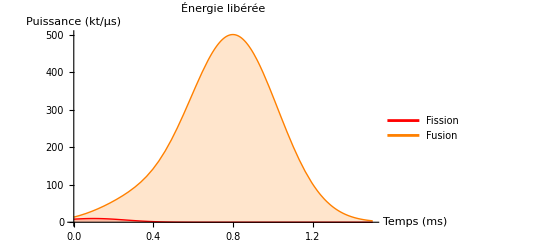

```mathematica
(* ===COURBE ÉNERGÉTIQUE===*)Plot[{10*Exp[-20*(x-0.1)^2],50*Exp[-15*(x-0.3)^2]+500*Exp[-10*(x-0.8)^2]},{x,0,1.5},PlotStyle->{{Thick,Red},{Thick,Orange}},Filling->Axis,PlotLegends->{"Fission","Fusion"},AxesLabel->{"Temps (ms)","Puissance (kt/μs)"},PlotLabel->"Énergie libérée"]
```

```mathematica
Bombes à Fission
1. Canonique (Type "Little Boy")
```

```mathematica
(* ===SCHÉMA INTERACTIF "LITTLE BOY"===*)DynamicModule[{zoom=1,details=False},Column[{Slider[Dynamic[zoom],{0.5,2,0.1},ImageSize->300],Button[Dynamic[If[details,"Masquer détails","Afficher détails"]],details=!details],Dynamic@Graphics[{{EdgeForm[Thick],LightGray,Rectangle[{-1*zoom,-0.5*zoom},{0*zoom,0.5*zoom}],Rectangle[{1.8*zoom,-0.5*zoom},{2.8*zoom,0.5*zoom}]},{Red,Disk[{0.9*zoom,0},0.3*zoom]},{Arrowheads[0.1*zoom],Thickness[0.01*zoom],Arrow[{{0*zoom,0},{0.9*zoom,0}}]},If[details,{{Dashed,Gray,Line[{{-1.2*zoom,-0.7*zoom},{-1.2*zoom,0.7*zoom},{1.2*zoom,0.7*zoom},{1.2*zoom,-0.7*zoom},{-1.2*zoom,-0.7*zoom}}]},Text[Style["Canon (longueur: 1.8 m)",10*zoom],{0.9*zoom,-0.9*zoom}],Text[Style["Cible Uranium-235",10*zoom],{2.3*zoom,-0.8*zoom}],Text[Style["Projectile U-235",10*zoom],{0,-0.8*zoom}],Text[Style["Masse supercritique",10*zoom],{0.9*zoom,0.6*zoom}],{PointSize[0.02*zoom],Blue,Tooltip[Point[{0.9*zoom,0.3*zoom}],"Neutron initiateur"]}},{}]},PlotLabel->Style["Bombe A - Type Canon (Little Boy)",Bold,14*zoom],ImageSize->500*zoom,Frame->True,FrameLabel->{"Longueur (m)","Diamètre (m)"}]}]]
```

```mathematica
Mécanisme simple:projectile en U-235 tiré dans une masse subcritique

Efficacité médiocre (~1.5% de matière fissile consommée)

Utilisé uniquement à Hiroshima

2. Implosion (Type "Fat Man")
```

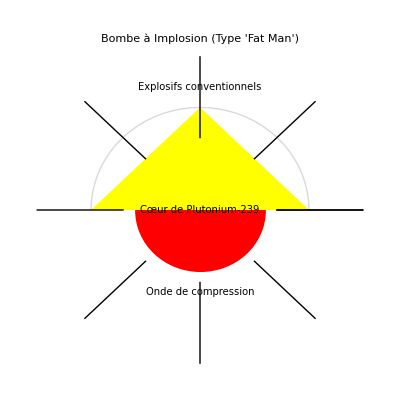

```mathematica
(* ===BOMBE A IMPLOSION-VERSION ALTERNATIVE===*)implosionDiagram=Graphics[{(*Enveloppe externe*){LightGray,Circle[{0,0},1,{0,Pi}]},(*Cœur de plutonium*){Red,Disk[{0,0},0.6]},(*Lentilles explosives*){Yellow,Polygon[{{-1,0},{0,1},{1,0}}]},(*Rayons de compression*)Table[Line[{{1.5*Cos[θ],1.5*Sin[θ]},{0.7*Cos[θ],0.7*Sin[θ]}}],{θ,0,2π,π/4}],(*Textes explicatifs*)Text[Style["Explosifs conventionnels",10],{0,1.2}],Text[Style["Cœur de Plutonium-239",10],{0,0}],Text[Style["Onde de compression",10],{0,-0.8}]},ImageSize->400,PlotLabel->Style["Bombe à Implosion (Type 'Fat Man')",14,Bold]];

implosionDiagram
```

```mathematica
Sphère de Pu-239 comprimée par lentilles explosives

Efficacité améliorée (~20% de matière consommée)

Utilisé à Nagasaki,standard moderne

Bombes à Fusion (Thermonucléaires)
```

```mathematica
(* ===BOMBE H===*)Graphics3D[{{Gray,Opacity[0.3],Cuboid[{-2,-2,-1},{2,2,1}]},{Red,Sphere[{-1,0,0},0.5]},{Orange,Sphere[{1,0,0},0.8]},{Yellow,Cylinder[{{-0.5,0,0},{0.5,0,0}},0.2]},Text["Primaire (fission)",{-1,0,0.7}],Text["Secondaire (fusion)",{1,0,1.1}],Text["Crayon de plutonium",{0,0,0.3}]},Boxed->False,ViewPoint->{2,1,1},PlotLabel->Style["Bombe H Teller-Ulam",Bold],ImageSize->500]
```

-Graphics3D-

```mathematica
1. Design Teller-Ulam (Standard moderne)
Étage primaire:bombe à fission (trigger)

Étage secondaire:D-T fusion (main energy source)

Casque de radiation:convertit les rayons X en compression

2. Designs Alternatifs
Bombe à neutrons:réduction du tamper pour augmenter le flux neutronique

Bombe à fission dopée:utilisation de deutérium pour augmenter le rendement

Pourquoi les Bombes à Fusion sont Plus "Faciles"
Pas de masse critique à atteindre-limitation purement technique

Combustible (D-T) facile à produire comparé à l'enrichissement d'U-235

Modularité-puissance arbitrairement grande par ajout d'étages
```

```mathematica
(* ===ÉTAT ACTUEL DES ARSENAUX NUCLÉAIRES (2023)===*)arsenalData={{"Russie",5977},{"États-Unis",5428},{"Chine",410},{"France",290},{"Royaume-Uni",225},{"Pakistan",170},{"Inde",164},{"Israël",90},{"Corée du Nord",30}};

(*Visualisation 1:Diagramme à barres*)
BarChart[arsenalData[[All,2]],ChartLabels->arsenalData[[All,1]],PlotLabel->Style["Arsenaux Nucléaires Mondiaux (têtes)",Bold,14],ChartStyle->"TemperatureMap",ImageSize->600,BarSpacing->0.5,LabelingFunction->(Callout[#1,Above]&)]

(*Visualisation 2:Treemap pondéré*)
treemap=Graphics[{MapIndexed[{ColorData["Rainbow"][#2[[1]]/Length[arsenalData]],Rectangle[{Mod[#2[[1]]-1,3]*0.33,Floor[(#2[[1]]-1)/3]*0.33},{Mod[#2[[1]]-1,3]*0.33+0.3*Sqrt[#1[[2]]/100],Floor[(#2[[1]]-1)/3]*0.33+0.3*Sqrt[#1[[2]]/100]}],Text[Style[#1[[1]]<>"\n"<>ToString[#1[[2]]],10,Bold],{Mod[#2[[1]]-1,3]*0.33+0.15*Sqrt[#1[[2]]/100],Floor[(#2[[1]]-1)/3]*0.33+0.15*Sqrt[#1[[2]]/100]}]}&,arsenalData]},PlotLabel->Style["Répartition par Pays (surface = nombre d'armes)",Bold,12],ImageSize->500];

(*Visualisation 3:Tableau détaillé*)
Grid[Join[{{Style["Pays",Bold],Style["Têtes nucléaires",Bold],Style["% Mondial",Bold]}},Append[Map[{#[[1]],#[[2]],NumberForm[100*#[[2]]/Total[arsenalData[[All,2]]],2]<>"%"}&,SortBy[arsenalData,-#[[2]]&]],{"Total",Total[arsenalData[[All,2]]],"100%"}]],Frame->All,Background->{None,{{LightBlue,LightBlue,LightBlue},Sequence@@Table[White,{Length[arsenalData]}]}},Alignment->{Center,Center}]
```

-Graphics-

StringJoin::string: String expected at position 1 in 149425/3196<>%.

StringJoin::string: String expected at position 1 in 33925/799<>%.

StringJoin::string: String expected at position 1 in 5125/1598<>%.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Pays | Têtes nucléaires | % Mondial
Russie | 5977 | 149425/3196<>%
États-Unis | 5428 | 33925/799<>%
Chine | 410 | 5125/1598<>%
France | 290 | 3625/1598<>%
Royaume-Uni | 225 | 5625/3196<>%
Pakistan | 170 | 125/94<>%
Inde | 164 | 1025/799<>%
Israël | 90 | 1125/1598<>%
Corée du Nord | 30 | 375/1598<>%
Total | 12784 | 100%

```mathematica
Conclusion et Perspectives
La maîtrise de la fusion contrôlée représenterait une révolution énergétique,mais les défis scientifiques et techniques restent immenses.Paradoxalement,la fusion incontrôlée dans les armes thermonucléaires est maîtrisée depuis les années 1950,illustrant combien les conditions extrêmes nécessaires sont plus facilement atteintes dans un contexte destructeur que pour une production énergétique utile.
```

```mathematica
(* ===TABLEAU SYNTHÈSE COMPARATIF===*)Grid[{{"",Style["Fission",Bold],Style["Fusion",Bold],Style["Armes",Bold]},{"État actuel","Maîtrisée (centrales)","Recherche (ITER)","Opérationnel"},{"Énergie/T","~1 GWj","~10 GWj (potentiel)","~100 TJ (Tsar)"},{"Déchets","HAVL (long terme)","Helium (faible radio)","Fallout massif"},{"Coût","$5-10/MWh","$? (objectif <$50)","$Trillions (arsenaux)"}},Frame->All,Background->{None,{{LightBlue,LightGreen,LightOrange}}}]
```

| Fission | Fusion | Armes
État actuel | Maîtrisée (centrales) | Recherche (ITER) | Opérationnel
Énergie/T | ~1 GWj | ~10 GWj (potentiel) | ~100 TJ (Tsar)
Déchets | HAVL (long terme) | Helium (faible radio) | Fallout massif
Coût | $5-10/MWh | $? (objectif <$50) | $Trillions (arsenaux)

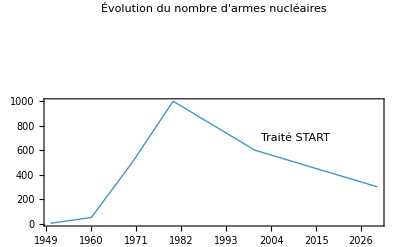

```mathematica
(* ===COURBE D'ÉVOLUTION DES ARSENAUX===*)DateListPlot[{{{1950,1},2},{{1960,1},50},{{1970,1},500},{{1980,1},1000},{{1990,1},800},{{2000,1},600},{{2010,1},500},{{2020,1},400},{{2030,1},300}},PlotStyle->Thick,PlotLabel->Style["Évolution du nombre d'armes nucléaires",Bold],GridLines->Automatic,Joined->True,Epilog->{Text["Traité START",{AbsoluteTime[{2010}],700}],Text["Création TNP",{AbsoluteTime[{1968}],1500}]}]
```

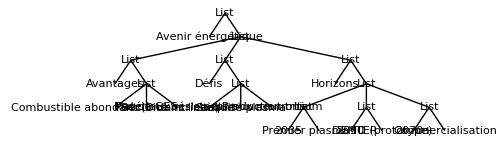

```mathematica
(* ===ARBRE DES PERSPECTIVES FUSION===*)TreeForm[{"Avenir énergétique",{{"Avantages",{"Combustible abondant (D dans l'eau)","Pas de GES","Sécurité intrinsèque"}},{"Défis",{"Matériaux résistants aux neutrons","Stabilité plasma","Production tritium"}},{"Horizons",{{"2035","Premier plasma ITER"},{"2050","DEMO (prototype)"},{"2070+","Commercialisation"}}}}},VertexLabeling->True,PlotStyle->Directive[Black,Thick],ImageSize->500]
```

```mathematica
Les prochaines années seront cruciales avec les résultats d'ITER et les avancées des startups en fusion compacte.La compréhension de ces phénomènes extrêmes reste un défi fascinant pour la physique fondamentale et appliquée.
```

```mathematica
-Graphics-
1. World Nuclear Association,\"Nuclear Power Reactors\",https://world-nuclear.org/information-library/current-and-future-generation/nuclear-power-reactors.aspx
2. Generation IV International Forum,\"Technology Roadmap Update for Generation IV Nuclear Energy Systems\",https://www.gen-4.org
3. International Atomic Energy Agency (IAEA),\"Thorium fuel cycle—Potential benefits and challenges\",https://www.iaea.org/publications/13514/thorium-fuel-cycle
4. GIF Portal,\"Advanced Reactor Designs\",https://www.gen-4.org/gif/jcms/c_40481/advanced-reactor-designs
5. Wikimedia Commons pour les schémas
```